# MOM Practice Sheet - 1

## Question - 1

```mathematica
x1 = 0;
y1 = 0.4;

x2 = 1+0.2*Log[4];
y2 = 0.4*ⅇ;

x3 = 1+0.2*Log[6];
y3 = 0.4*ⅇ;

x4 = 0.2*Log[3];
y4 = 0.4;

x5 = 0;
y5 = 0;

x6 = 1;
y6 = 0;

x7 = 1;
y7 = 1;

x8 = 0;
y8 = 1;
```

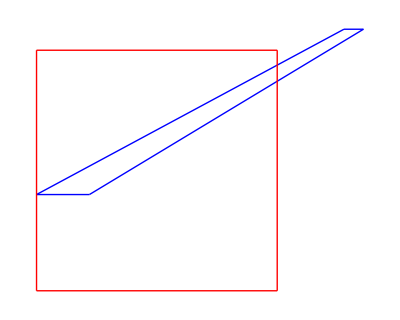

```mathematica
Graphics[{
   Blue, Thick, 
   Line[{{x1, y1}, {x2, y2}}],
   Line[{{x2, y2}, {x3, y3}}],
   Line[{{x3, y3}, {x4, y4}}],
   Line[{{x4, y4}, {x1, y1}}],  (* notice I fixed x1,y1 to x4,y4 order *)

   Red, Thick,
   Line[{{x5, y5}, {x6, y6}}],
   Line[{{x6, y6}, {x7, y7}}],
   Line[{{x7, y7}, {x8, y8}}],
   Line[{{x8, y8}, {x5, y5}}]   (* fixed your typo: {x5, x5} -> {x5, y5} *)
}]
```

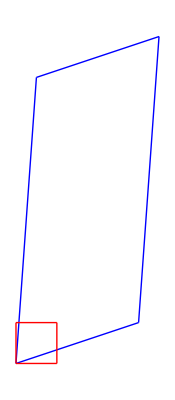

```mathematica
x1 = 0;
y1 = 0;

x2 = 3;
y2 = 1;

x3 = 3.5;
y3 = 8;

x4 = 0.5;
y4 = 7;

x5 = 0;
y5 = 0;

x6 = 1;
y6 = 0;

x7 = 1;
y7 = 1;

x8 = 0;
y8 = 1;
Graphics[{
   Blue, Thick, 
   Line[{{x1, y1}, {x2, y2}}],
   Line[{{x2, y2}, {x3, y3}}],
   Line[{{x3, y3}, {x4, y4}}],
   Line[{{x4, y4}, {x1, y1}}],  (* notice I fixed x1,y1 to x4,y4 order *)

   Red, Thick,
   Line[{{x5, y5}, {x6, y6}}],
   Line[{{x6, y6}, {x7, y7}}],
   Line[{{x7, y7}, {x8, y8}}],
   Line[{{x8, y8}, {x5, y5}}]   (* fixed your typo: {x5, x5} -> {x5, y5} *)
}]
```

```mathematica
A = {{200, -50}, 
     {-50, 100}};
     
B = {{Cos[12.3], Sin[12.3]}, 
     {Sin[12.3], Cos[12.3]}};
MatrixForm[A]
Eigenvalues[A]

FullSimplify[Transpose[B].A.B]//MatrixForm
```

(200 | -50
-50 | 100)

{50 (3+√2),50 (3-√2)}

(218.466 | -126.184
-126.184 | 132.324)

```mathematica
Solve[ⅇ^((-ζ*π)/((1-ζ^2)^0.5))-0.254==0,ζ]

ωn = FullSimplify[π/(3*(1-0.4^2)^0.5)]
T = 1/(2*0.4*ωn)
K = ωn^2*T
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ζ→0.399833}}

1.14259

1.09401

1.42823

```mathematica
900/(Cosh[47.87*50*10^-3])
```

162.998

```mathematica
((250*110*10^-3)/(20*6*10^-4))^0.5
```

47.8714

```mathematica
(20*250*6*10^-4*0.11)^0.5*-900
```

-517.011

```mathematica
Tanh[1.1236]
```

0.808817

```mathematica
FindRoot[24.1*L - Tanh[37.08*L], {L, 1, 10}]
```

{L→0.036187}

```mathematica
a = (Sinh[37.08*0.0351]+ 0.038*Cosh[37.08*0.0351])/(Cosh[37.08*0.0351]+ 0.038*Sinh[37.08*0.0351])
```

0.871558

```mathematica
a*26.96
```

23.4972

```mathematica
(393*0.001^2*100*π^2*0.25*0.001)^0.5*(25)*Tanh[25*0.001*((100*π*0.001)/(393*π*0.25*0.001^2))^0.5]
```

0.16314

```mathematica
d = 10^-3;
h = 100;
P = π*d;
k = 393;
L = 25*10^-3;
Tb = 100;
Ac = π*d^2/4
M = (h*P*k*Ac*Tb)^0.5
m = ((h*P)/(k*Ac))^0.5
q = M*(Cosh[m*L])/(Sinh[m*L])
```

π/4000000

0.0984728

31.9032

0.148598

```mathematica
((Cosh[119.5*40*10^-3]+1)/Sinh[119.5*40*10^-3])*1.314
```

1.33625

```mathematica
eqn1 = c1+c2 ==25
eqn2 = c1*ⅇ^(119.52*0.04) + ⅇ^(-119.52*0.04)*c2 == -25
Solve[{eqn1,eqn2},{c1,c2}]
25*140*π*10^-6*119.52
```

c1+c2==25

119.2 c1+0.00838928 c2==-25

{{c1→-0.211507,c2→25.2115}}

1.31419

```mathematica
0.2116857947999691-25.21168579479997
```

-25.

```mathematica
N1 = {{l1, m1, n1}};
N1//MatrixForm
N2 = {{l2},{m2},{n2}};
N2 // MatrixForm

σ = {{σxx,σxy,σxz}, 
     {σxy,σyy,σyz}, 
     {σxz,σyz,σzz}};
MatrixForm[σ]

σXY = N1.σ.N2
FullSimplify[σXY]

ϵ = {{ϵxx,ϵxy}, 
     {ϵxy,ϵyy}};
Q = {{Cos[θ],-Sin[θ]}, 
     {Sin[θ],Cos[θ]}};
Q' = Transpose[Q]

ϵ//MatrixForm
Q//MatrixForm
Q'//MatrixForm
```

# Transformation of Stress in 3D

```mathematica
σ = {{σxx,σxy,σxz}, 
     {σxy,σyy,σyz}, 
     {σxz,σyz,σzz}};
MatrixForm[σ]

N1 = {{l1, m1, n1}};
N1//MatrixForm
N2 = {{l1},{m1},{n1}};
N2 // MatrixForm
N3 = {{l2},{m2},{n2}};
N3 // MatrixForm

σXX = N1.σ.N2;
σXY = N1.σ.N3;
FullSimplify[σXX]
FullSimplify[σXY]
```

(σxx | σxy | σxz
σxy | σyy | σyz
σxz | σyz | σzz)

(l1 | m1 | n1)

(l1
m1
n1)

(l2
m2
n2)

{{l1^2 σxx+2 l1 (m1 σxy+n1 σxz)+m1^2 σyy+2 m1 n1 σyz+n1^2 σzz}}

{{l2 m1 σxy+l2 n1 σxz+l1 (l2 σxx+m2 σxy+n2 σxz)+m1 m2 σyy+m2 n1 σyz+m1 n2 σyz+n1 n2 σzz}}

# Strain Questions (Boresi & Schmidt)

## 2.54, 2.55

```mathematica
ϵxx = 0.00180;
ϵyy = -0.00108;
ϵxy = -0.00110;
θ = ArcTan[3/4]

ϵ = {{ϵxx,ϵxy}, 
     {ϵxy,ϵyy}};
     
λ = Eigenvalues[ϵ]
(*Q = {{Cos[θ],-Sin[θ]}, 
     {Sin[θ],Cos[θ]}};
Q' = Transpose[Q]

ϵ//MatrixForm
Q//MatrixForm
Q'//MatrixForm

ϵ' = Q'.ϵ
ϵ'' = FullSimplify[ϵ'.Q]
ϵ''//MatrixForm*)
```

```mathematica
σ = {{50,5,-30}, 
     {5,-30,0},{-30, 0, 20}};
σ//MatrixForm

N1 = {{1/3^0.5},{1/3^0.5},{1/3^0.5}};
N1//MatrixForm


a = FullSimplify[σ.N1]

   
(*λ = Eigenvalues[σ]
Eigenvectors[σ]*)
```

(50 | 5 | -30
5 | -30 | 0
-30 | 0 | 20)

(0.57735
0.57735
0.57735)

{{14.4338},{-14.4338},{-5.7735}}

```mathematica
σ = {{-2/3,-3,0}, 
     {-3,-2/3,0},{0, 0, 4/3}};
λ = Eigenvalues[σ]
```

{-11/3,7/3,4/3}

```mathematica
a = {{1},{0},{1}}
b = {{0, 1, 1}}
a//MatrixForm
b//MatrixForm
c =a.b
c//MatrixForm
```

{{1},{0},{1}}

{{0,1,1}}

(1
0
1)

(0 | 1 | 1)

{{0,1,1},{0,0,0},{0,1,1}}

(0 | 1 | 1
0 | 0 | 0
0 | 1 | 1)